```mathematica
InverseNull[n_]:=First[Select[realyNullAtomKeys,allGraphs[#,"colofourrealnull"]==n&]]
```

```mathematica
Select[Table[Simplify[ allGraphs[k,"comp"][allGraphs[k,"colofourrealnull"],0]],{k,Keys[allGraphs]}],Length[ListofVars[#]]==2&];
```

```mathematica
lattice=Map[InverseNull[#[[1]]]->InverseNull[#[[2]]]&, Select[Table[Simplify[ allGraphs[k,"comp"][allGraphs[k,"colofourrealnull"],0]],{k,Keys[allGraphs]}],Length[ListofVars[#]]==2&]]
```

{0→486,26→728,72→728,18→666,162→666,168→728,218→728,6→546,54→546,2→488,486→666,488→728,546→728,666→728,486→546,486→488,0→162,2→218,54→218,6→168,162→218,162→168,0→54,18→72,54→72,0→18,2→26,6→26,18→26,0→6,0→2}

```mathematica
direct=Select[
Flatten[
Table[
Table[
{
If[ToString[allGraphs[c[[1]],"comp"]]=="Greater",
 k->c[[2]]
];
If[ToString[allGraphs[c[[2]],"comp"]]=="Greater",
k->c[[1]]
]
}
,{c,allGraphs[k,"children"]}
]
,
{k,Keys[allGraphs]}
]],
ToString[#]≠"Null"&];
```

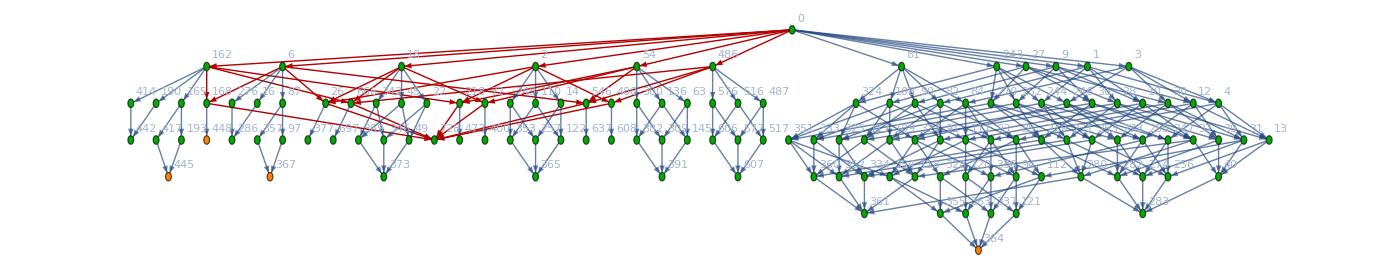

```mathematica
Graph[DeleteDuplicates[Join[lattice,direct]], 
VertexLabels->Table[k->Tooltip[k,
TableForm[
{
allGraphs[k,"graph"],
allGraphs[k,"colofourrealnull"],
allGraphs[k,"colofour"]
}
]],{k,DeleteDuplicates[Flatten[Map[{#[[1]],#[[2]]}&,Join[lattice,direct]]]]}],
VertexStyle->Table[k->ColourForKey[allGraphs,k],{k,Keys[allGraphs]}],
GraphHighlight->lattice,
GraphLayout->"LayeredDigraphEmbedding",
ImageSize->1400]
```